# Time Indepent Schrodinger Equation

## Defining the Equation We are studying the behavior of the time independent Schrodinger equation in a semi-infinite triangular potential shown below.

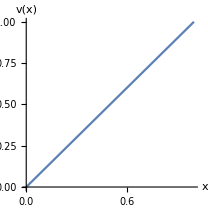

```mathematica
Clear["Global '*"];
(* We set the boundary condition that ψ(0) = 0, so we can use this as our potential *)
v[x_] := x;

Plot[v[x], {x, 0, 1}, AspectRatio->1, AxesLabel->{"x","v(x)"}]
```

We use the built in NDSolve function to solve the Schrodinger equation.  The wave function takes in values for Energy and Length and returns a plottable function: ψ(x)

psi[E_,L_] := Block[{soln,ψ,x,eq},
soln = NDSolve[{(-1/2)ψ''[x]+v[x]*ψ[x]==E*ψ[x],ψ[0]==0,ψ'[0]==1},ψ,{x,0,L}];
eq = ψ/.soln[[1]];
Return[eq];
];

Let us test this function to make sure that it is working properly.

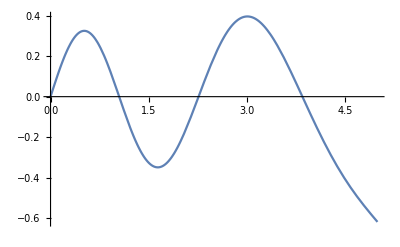

```mathematica
p = psi[5,5];
Plot[p[x],{x,0,5}]
```

This function appears to meet the boundary condition, ψ(x) = 0, and has the characteristic sinusoidal behavior, so it seems our function is working.

## Studying the Equation Looking at the behavior of the equation as a function of energy. The domain of the function can also be varied, by manipulating L.

```mathematica
Manipulate[
ps =psi[energy, L];
Plot[ps[x],{x,0,L},
PlotRange->{{0,L},{-1,1}},
Frame->True,FrameLabel->{"x","ψ[x]"}],
{{energy,7,"Energy"},0,25},
{{L, 10, "L"}, 5, 20}
]
```

## Finding the Eigenvalues In order to use the FindRoot function on an NDSolve, we must define a new function, psi2, that returns a function ψ(x) for a given value of energy. We then use the FindRoot function to find the eigenvalues of the energy.

```mathematica
Clear[ψ]
(* Defines the function that FindRoot will use *)
psi2[E_?NumberQ] :=ψ/.First@NDSolve[{
(-1/2)ψ''[x]+x*ψ[x]==E*ψ[x],
ψ[0]==0,
ψ'[0]==1
},
ψ,{x,0,10}];
```

Again, let us test to make sure that this function is working properly before we call FindRoot. We will create a function corresponding to E = 5 and compare function values to the first test graph that also used E = 5.

```mathematica
p2=psi2[5];
```

```mathematica
p2[1]
```

0.0468054

```mathematica
p2[2]
```

-0.212455

```mathematica
p2[3]
```

0.395564

These values coincide with the values of ψ(1), ψ(2), and ψ(3) in the test graph in the first section, so it appears that our psi2 function is also working properly. Now we can call FindRoot to find the first few eigenvalues of energy.  We first plot psi vs energy at a fixed L value of 10.  The roots on this plot are the eigenvalues of energy, giving us an idea of their values.

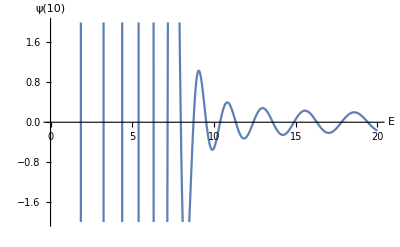

```mathematica
Plot[psi2[y][10], {y,1,20}, PlotRange->{-2,2},AxesLabel->{"E",HoldForm[ψ[10]]}]
```

Next we call FindRoot to find the first few eigenvalues of energy.

```mathematica
eig1 = en/.FindRoot[psi2[en][10],{en,1}]
```

1.85576

```mathematica
eig2 = en/.FindRoot[psi2[en][10],{en,3}]
```

3.24461

```mathematica
eig3 = en/.FindRoot[psi2[en][10],{en,4}]
```

4.38167

```mathematica
eig4 = en/.FindRoot[psi2[en][10],{en,5}]
```

5.38661

```mathematica
eig5 = en/.FindRoot[psi2[en][10],{en,6}]
```

6.30526

Below is a plot of the wave function with energy fixed at these eigenvalues.

```mathematica
Manipulate[
ps=psi[energy,L];
Plot[ps[x],{x,0,L},
PlotRange->{{0,L},{-1,1}},
Frame->True,FrameLabel->{"x","ψ[x]"}],
{{energy,eig1,"Energy"},{eig1,eig2,eig3,eig4,eig5}},
{{L,15,"L"},15,100}
]
```

We see that at these eigenvalues the function demonstrates the desired behavior of approaching zero as x approachs infinity, however it falls off at large values of x.

## Normalizing the Wavefunction We integrate ψ(x) from 0 up until right before the solution diverges, making the estimation that the horizontal asymptote will continue to ∞. If the result is 1, then the function is normalized. If it is not, then we must add a normalization constant in front of the wavefunction. Since the function is its own complex conjugate, we can substitute ψ^2 for for ψ*ψ.

0.5

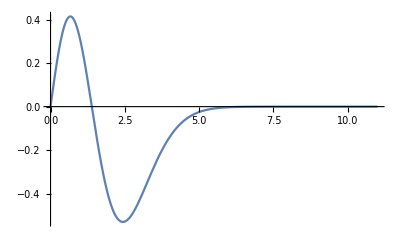

```mathematica
ps2=psi[eig2,11];
NIntegrate[ps2[x]^2,{x,0,11}]
Plot[ps2[x],{x,0,11}]
```

Since the function integrated to .5, we must add a normalization constant of  √2 to the wavefunction.

1.

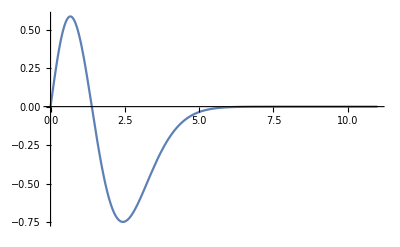

```mathematica
NIntegrate[(Sqrt[2]*ps2[x])^2,{x,0,11}]
Plot[Sqrt[2]*ps2[x],{x,0,11}]
```

We now get the desired result of 1, so our normalized wavefunction!

## Comparing the Results We now compare the results of our solution computed with NDSolve to the analytical solution given by DSolve.

```mathematica
analy[E_,L_] := Block[{soln,ψ,x,eq},
soln = DSolve[{(-1/2)ψ''[x]+v[x]*ψ[x]==E*ψ[x],ψ[0]==0,ψ'[0]==1},ψ,{x,0,L}];
eq = ψ/.soln[[1]];
Return[eq];
];
```

```mathematica
Manipulate[
an =analy[energy, L];
Plot[an[x],{x,0,L},
PlotRange->{{0,L},{-1,1}},
Frame->True,FrameLabel->{"x","ψ[x]"}],
{{energy,7,"Energy"},0,25},
{{L, 10, "L"}, 0, 20}
]
```

This graph of the analytical solution looks similar to our numerical solution. We confirm this by plotting the error.

```mathematica
Manipulate[
anerr = analy[energy, L];
pserr = psi[energy, L];
Plot[Abs[anerr[x] - pserr[x]] ,{x,0,L},
PlotRange->{{0,L},{-.01,1}},
Frame->{{True,False},{True,False}},FrameLabel->{"x","ψ[x]"}],
{{energy,7,"Energy"},0,25},
{{L, 15, "L"}, 0, 20}
]
```

The error is zero in the appropriate range. Now we’ll compare the eigenvalues.

```mathematica
analy2[E_?NumberQ] :=ψ/.First@NDSolve[{
(-1/2)ψ''[x]+x*ψ[x]==E*ψ[x],
ψ[0]==0,
ψ'[0]==1
},
ψ,{x,0,10}];
```

```mathematica
aneig1 = en/.FindRoot[analy2[en][10],{en,1}]
```

1.85576

```mathematica
aneig2 = en/.FindRoot[analy2[en][10],{en,3}]
```

3.24461

```mathematica
aneig3 = en/.FindRoot[analy2[en][10],{en,4}]
```

4.38167

```mathematica
aneig4 = en/.FindRoot[analy2[en][10],{en,5}]
```

5.38661

```mathematica
aneig5 = en/.FindRoot[analy2[en][10],{en,6}]
```

6.30526

Once again we plot psi with energy fixed at these eigenvalues.

```mathematica
Manipulate[
an=analy[energy,L];
Plot[an[x],{x,0,L},
PlotRange->{{0,L},{-1,1}},
Frame->{{True,False},{True,False}},FrameLabel->{"x","ψ[x]"}],
{{energy,eig1,"Energy"},{aneig1,aneig2,aneig3,aneig4,aneig5}},
{{L,15,"L"},15,100}
]
```

These look very similar to the solutions generated by our approximation.  Again we look at the error.

{0.,0.,0.,0.,0.}

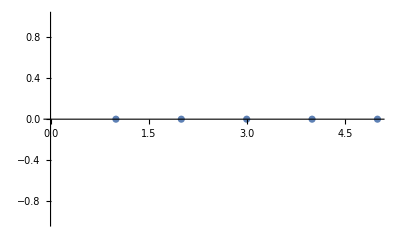

```mathematica
error = {Abs[aneig1-eig1],Abs[aneig2-eig2], Abs[aneig3-eig3], Abs[aneig4-eig4],Abs[aneig5-eig5]}
ListPlot[error]
```

So the eigenvalues calculated from the analytical solution are the same as those calculated from our numerical solution!

# Compairing Methods We compare the results our method of finding eigenvalues to Newton’s, Brent’s, and the secant methods. First we look at the efficieny of these different methods.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

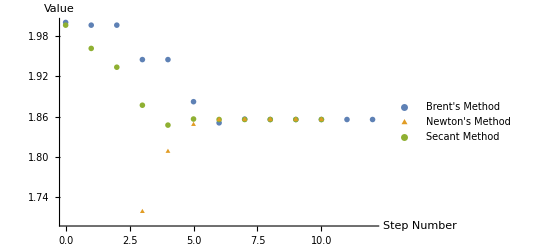

Newton's method required 36 evalutions and 11 steps. Brent's method required 15, evaluations and 13steps. The secant method required 27 evaluations and 11 steps.

```mathematica
brent={};
brentEvals=0;
i=0;
FindRoot[psi2[z][10],{z,1,2}, EvaluationMonitor:>brentEvals++,Method->"Brent",StepMonitor:> AppendTo[brent, {i++, z}]];

newton={};
newtonEvals=0;
i=0;
FindRoot[psi2[z][10],{z,1}, EvaluationMonitor:>newtonEvals++,StepMonitor:> AppendTo[newton, {i++, z}]];

secant={};
secantEvals=0;
i=0;
FindRoot[psi2[z][10],{z,1,2}, EvaluationMonitor:>secantEvals++,Method->"Secant",StepMonitor:> AppendTo[secant, {i++, z}]];

ListPlot[{brent, newton, secant}, PlotMarkers->{•,▲,◼},PlotLegends->{"Brent's Method","Newton's Method","Secant Method"},AxesLabel->{"Step Number", "Value"}]
Print["Newton's method required ",newtonEvals," evalutions and ", Length[newton]," steps. Brent's method required ",brentEvals,", evaluations and ",Length[brent],"steps. The secant method required ", secantEvals, " evaluations and ",Length[secant]," steps."]
```

Next we look at and plot the difference in eigenvalues when changing the precision of NDSolve.

```mathematica
Clear[psi2];
Manipulate[
psi2[E_?NumberQ] :=ψ/.First@NDSolve[{
(-1/2)ψ''[x]+x*ψ[x]==E*ψ[x],
ψ[0]==0,
ψ'[0]==1
},
ψ,{x,0,10}, PrecisionGoal->precision];

e1 = en/.FindRoot[psi2[en][10],{en,1}];
  e2 = en/.FindRoot[psi2[en][10],{en,3}];
  e3 = en/.FindRoot[psi2[en][10],{en,4}];
  e4 = en/.FindRoot[psi2[en][10],{en,5}];
  e5 = en/.FindRoot[psi2[en][10],{en,6}];

ListPlot[{{Abs[e1-aneig1],Abs[e2-aneig2],Abs[e3-aneig3],Abs[e4-aneig4],Abs[e5-aneig5]}},  Frame->{{True,False},{True,False}},  FrameLabel->{"Eigenvalue Number", "Error"},  ImageSize->Medium],
{{precision, 8, "Precision"}, {8,10,12}}
]
(*this plot shows the error of the numerical calculation of the eigenvalues when using different values for PrecisionGoal*)
```

Next we look at the error of psi, depending on the precision values.

```mathematica
psi3[E_,L_, precise_] := Block[{soln,ψ,x,eq},
soln = NDSolve[{(-1/2)ψ''[x]+v[x]*ψ[x]==E*ψ[x],ψ[0]==0,ψ'[0]==1},ψ,{x,0,L}, PrecisionGoal->precise];
eq = ψ/.soln[[1]];
Return[eq];
];

Manipulate[an2=analy[energy,15];
psiPlot1=psi3[energy,15,8];
psiPlot2=psi3[energy, 15, 10];
psiPlot3=psi3[energy,15,12];
Plot[{Abs[an2[x]-psiPlot1[x]],Abs[an2[x]-psiPlot2[x]],Abs[an2[x]-psiPlot3[x]]},{x,0,15},PlotRange->{{0,15},{0,1}},Frame->{{True,False},{True,False}},FrameLabel->{"x","Error"}, PlotLegends->{"Precision: 8 digits","Precision: 10 digits","Precisiont: 12 digits"}],{{energy,aneig3,"Energy Eigenvalue"},{aneig1,aneig2,aneig3,aneig4,aneig5}}]
```